# Velocity Dispersion and Power Spectra

## Circular Test Ring

#### NFW parameters = {417.0 * pow(10,3) * mau * secyr, 36.54 * kpcau, 90.0 * pi / 180, 1.0, 1.0, 1.0} (NO TRIAXIALITY) 1000 test particles r0 = 15 kpc 100 timesteps of 1 Myr each

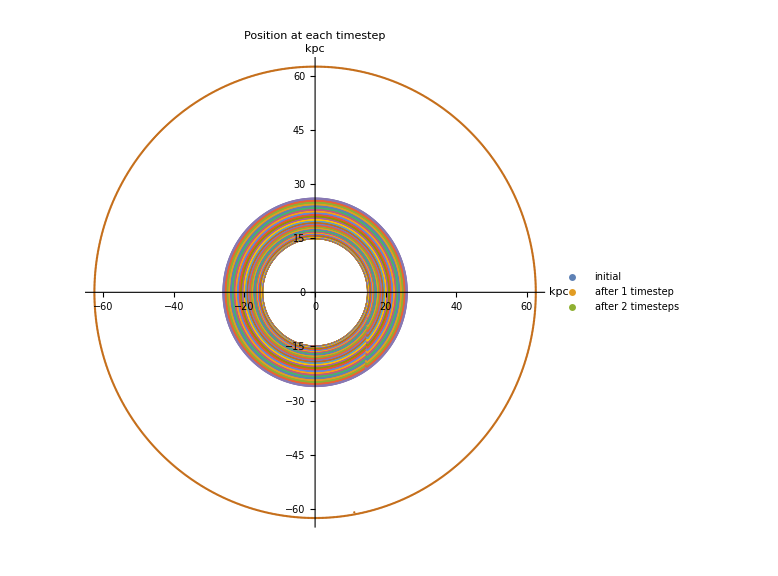

```mathematica
ch1pos = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",1;;1000,1;;2}];
ch1pos2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",1000;;2000,1;;2}];
ch1pos3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",2000;;3000,1;;2}];
ch1pos4 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",3000;;4000,1;;2}];
ch1pos5 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",4000;;5000,1;;2}];
ch1pos6 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",5000;;6000,1;;2}];
ch1pos7 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",6000;;7000,1;;2}];
ch1pos8 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",7000;;8000,1;;2}];
ch1pos9 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",8000;;9000,1;;2}];
ch1pos10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",9000;;10000,1;;2}];
ch1pos11 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",10000;;11000,1;;2}];
ch1pos12 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",11000;;12000,1;;2}];
ch1pos13 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",12000;;13000,1;;2}];
ch1pos14 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",13000;;14000,1;;2}];
ch1pos15 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",14000;;15000,1;;2}];
ch1pos16 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",15000;;16000,1;;2}];
ch1pos17 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",16000;;17000,1;;2}];
ch1pos18 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",17000;;18000,1;;2}];
ch1pos19 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",18000;;19000,1;;2}];
ch1pos20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",19000;;20000,1;;2}];
ch1pos21 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",20000;;21000,1;;2}];
ch1pos22 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",21000;;22000,1;;2}];
ch1pos23 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",22000;;23000,1;;2}];
ch1pos24 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",23000;;24000,1;;2}];
ch1pos25 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",24000;;25000,1;;2}];
ch1pos26 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",25000;;26000,1;;2}];
ch1pos27 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",26000;;27000,1;;2}];
ch1pos28 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",27000;;28000,1;;2}];
ch1pos29 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",28000;;29000,1;;2}];
ch1pos30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",29000;;30000,1;;2}];
ch1pos31 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",30000;;31000,1;;2}];
ch1pos32 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",31000;;32000,1;;2}];
ch1pos33 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",32000;;33000,1;;2}];
ch1pos34 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",33000;;34000,1;;2}];
ch1pos35 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",34000;;35000,1;;2}];
ch1pos36 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",35000;;36000,1;;2}];
ch1pos100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",99000;;100000,1;;2}];

ch1vel = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",1;;1000,4;;5}];
ch1vel2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",1000;;2000,4;;5}];
ch1vel3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",2000;;3000,4;;5}];
ch1vel4 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",3000;;4000,4;;5}];
ch1vel5 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",4000;;5000,4;;5}];
ch1vel6 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",5000;;6000,4;;5}];
ch1vel7 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",6000;;7000,4;;5}];
ch1vel8 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",7000;;8000,4;;5}];
ch1vel9 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",8000;;9000,4;;5}];
ch1vel10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",9000;;10000,4;;5}];
ch1vel11 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",10000;;11000,4;;5}];
ch1vel12 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",11000;;12000,4;;5}];
ch1vel13 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",12000;;13000,4;;5}];
ch1vel14 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",13000;;14000,4;;5}];
ch1vel15 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",14000;;15000,4;;5}];
ch1vel16 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",15000;;16000,4;;5}];
ch1vel17 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",16000;;17000,4;;5}];
ch1vel18 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",17000;;18000,4;;5}];
ch1vel19 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",18000;;19000,4;;5}];
ch1vel20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",19000;;20000,4;;5}];
ch1vel21 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",20000;;21000,4;;5}];
ch1vel22 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",21000;;22000,4;;5}];
ch1vel23 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",22000;;23000,4;;5}];
ch1vel24 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",23000;;24000,4;;5}];
ch1vel25 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",24000;;25000,4;;5}];
ch1vel26 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",25000;;26000,4;;5}];
ch1vel27 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",26000;;27000,4;;5}];
ch1vel28 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",27000;;28000,4;;5}];
ch1vel29 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",28000;;29000,4;;5}];
ch1vel30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",29000;;30000,4;;5}];
ch1vel31 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",30000;;31000,4;;5}];
ch1vel32 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",31000;;32000,4;;5}];
ch1vel33 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",32000;;33000,4;;5}];
ch1vel34 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",33000;;34000,4;;5}];
ch1vel35 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",34000;;35000,4;;5}];


ch1AM = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",1,1;;1000}];
ch1AM2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",2,1;;1000}];
ch1AM3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",3,1;;1000}];
ch1AM4 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",4,1;;1000}];
ch1AM5 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",5,1;;1000}];
ch1AM6 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",6,1;;1000}];
ch1AM7 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",7,1;;1000}];
ch1AM8 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",8,1;;1000}];
ch1AM9 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",9,1;;1000}];
ch1AM10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",10,1;;1000}];
ch1AM11 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",11,1;;1000}];
ch1AM12 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",12,1;;1000}];
ch1AM13 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",13,1;;1000}];
ch1AM14 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",14,1;;1000}];
ch1AM15 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",15,1;;1000}];
ch1AM16 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",16,1;;1000}];
ch1AM17 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",17,1;;1000}];
ch1AM18 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",18,1;;1000}];
ch1AM19 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",19,1;;1000}];
ch1AM20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",20,1;;1000}];
ch1AM21 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",21,1;;1000}];
ch1AM22 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",22,1;;1000}];
ch1AM23 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",23,1;;1000}];
ch1AM24 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",24,1;;1000}];
ch1AM25 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",25,1;;1000}];
ch1AM26 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",26,1;;1000}];
ch1AM27 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",27,1;;1000}];
ch1AM28 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",28,1;;1000}];
ch1AM29 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",29,1;;1000}];
ch1AM30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",30,1;;1000}];
ch1AM31 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",31,1;;1000}];
ch1AM32 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",32,1;;1000}];
ch1AM33 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",33,1;;1000}];
ch1AM34 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",34,1;;1000}];
ch1AM35 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",35,1;;1000}];
ch1AM36 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",36,1;;1000}];

ch1SD = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/SD1.csv",{"Data",1;;101,1;;2}];



ch1posgraph = ListPlot[{ch1pos,ch1pos2,ch1pos3,ch1pos4,ch1pos5,ch1pos6,ch1pos7,ch1pos8,ch1pos9,ch1pos10,ch1pos11,ch1pos12,ch1pos13,ch1pos14,ch1pos15,ch1pos16,ch1pos17,ch1pos18,ch1pos19,ch1pos20,ch1pos21,ch1pos22,ch1pos23,ch1pos24,ch1pos25,ch1pos26,ch1pos27,ch1pos28,ch1pos29,ch1pos30,ch1pos31,ch1pos32,ch1pos33,ch1pos34,ch1pos35,ch1pos100},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 1 timestep","after 2 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

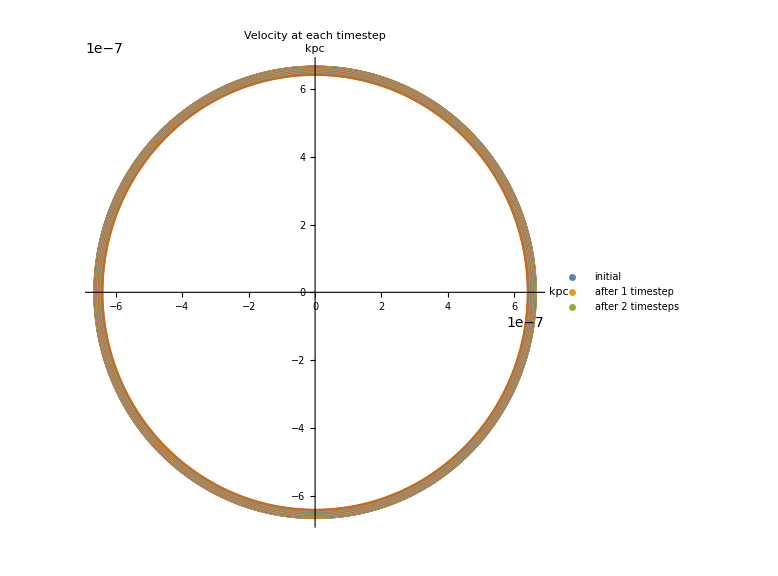

```mathematica
ch1velgraph = ListPlot[{ch1vel,ch1vel2,ch1vel3,ch1vel4,ch1vel5,ch1vel6,ch1vel7,ch1vel8,ch1vel9,ch1vel10,ch1vel11,ch1vel12,ch1vel13,ch1vel14,ch1vel15,ch1vel16,ch1vel17,ch1vel18,ch1vel19,ch1vel20,ch1vel21,ch1vel22,ch1vel23,ch1vel24,ch1vel25,ch1vel26,ch1vel27,ch1vel28,ch1vel29,ch1vel30,ch1vel31,ch1vel32,ch1vel33,ch1vel34,ch1vel35,ch1vel36},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 1 timestep","after 2 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel-> "Velocity at each timestep"]
```

#### Velocity Dispersion

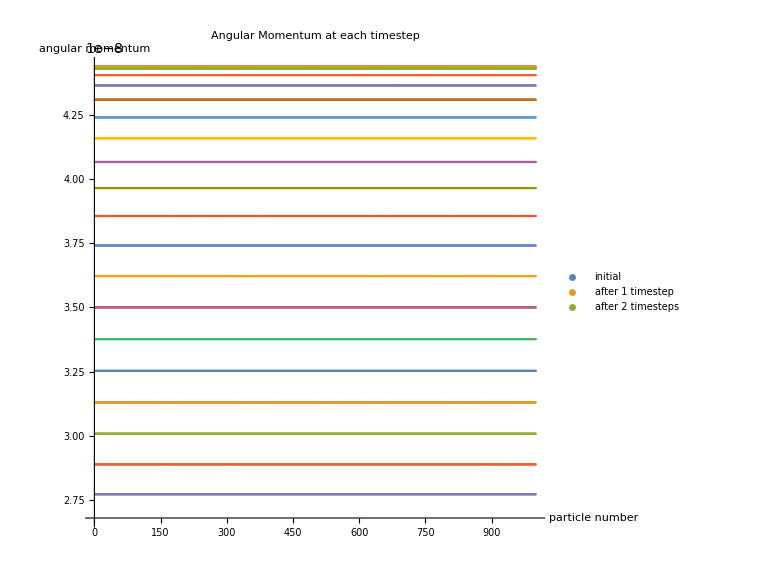

```mathematica
ch1AMgraph = ListPlot[{ch1AM,ch1AM2,ch1AM3,ch1AM4,ch1AM5,ch1AM6,ch1AM7,ch1AM8,ch1AM9,ch1AM10,ch1AM11,ch1AM12,ch1AM13,ch1AM14,ch1AM15,ch1AM16,ch1AM17,ch1AM18,ch1AM19,ch1AM20},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 1 timestep","after 2 timesteps"},AxesLabel->{"particle number","angular momentum"}, PlotLabel-> "Angular Momentum at each timestep"]
```

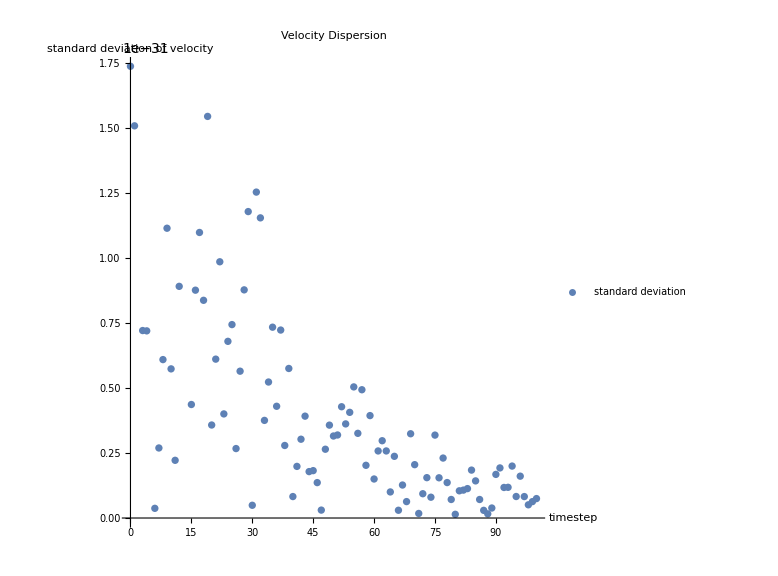

```mathematica
ch1SDgraph = ListPlot[{ch1SD},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"standard deviation"},AxesLabel->{"timestep","standard deviation of velocity"}, PlotLabel-> "Velocity Dispersion"]
```

#### Version 2: timestep/10, fewer particles NFW parameters = {417.0 * pow(10,3) * mau * secyr, 36.54 * kpcau, 90.0 * pi / 180, 1.0, 1.0, 1.0} (NO TRIAXIALITY) 10 test particles r0 = 15 kpc 100 timesteps of 100, 000 years each

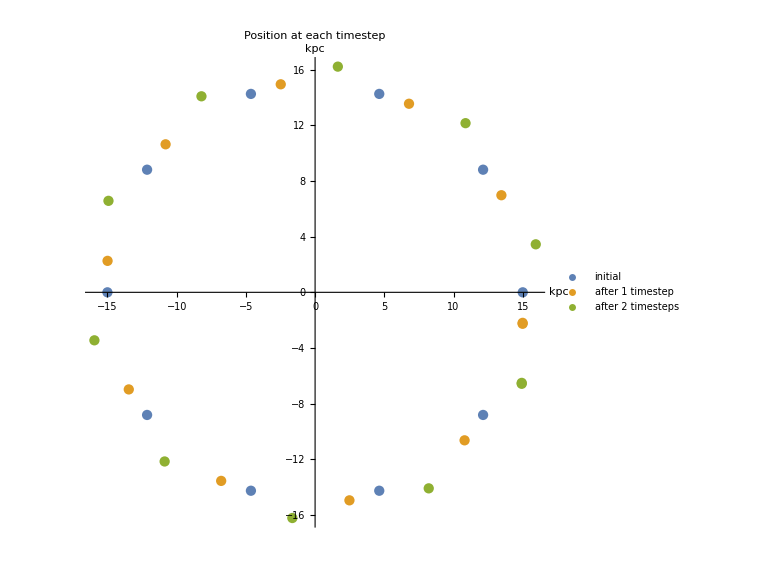

```mathematica
ch2pos1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",1;;10,1;;2}];
ch2pos2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",10;;20,1;;2}];
ch2pos3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",20;;30,1;;2}];
ch2pos4 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",30;;40,1;;2}];
ch2pos5 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",40;;50,1;;2}];
ch2pos6 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",50;;60,1;;2}];
ch2pos7 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",60;;70,1;;2}];
ch2pos8 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",70;;80,1;;2}];
ch2pos9 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",80;;90,1;;2}];
ch2pos10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",90;;100,1;;2}];
ch2pos11 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",100;;110,1;;2}];
ch2pos12 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",110;;120,1;;2}];
ch2pos13 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",120;;130,1;;2}];
ch2pos14 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",130;;140,1;;2}];
ch2pos15 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",140;;150,1;;2}];
ch2pos16 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",150;;160,1;;2}];
ch2pos17 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",160;;170,1;;2}];
ch2pos18 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",170;;180,1;;2}];
ch2pos19 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",180;;190,1;;2}];
ch2pos20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",190;;200,1;;2}];
ch2pos21 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",200;;210,1;;2}];
ch2pos22 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",210;;220,1;;2}];
ch2pos23 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",220;;230,1;;2}];
ch2pos24 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",230;;240,1;;2}];
ch2pos25 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",240;;250,1;;2}];
ch2pos26 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",250;;260,1;;2}];
ch2pos27 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",260;;270,1;;2}];
ch2pos28 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",270;;280,1;;2}];
ch2pos29 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",280;;290,1;;2}];
ch2pos30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",290;;300,1;;2}];
ch2pos31 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",300;;310,1;;2}];
ch2pos32 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",310;;320,1;;2}];
ch2pos33 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",320;;330,1;;2}];
ch2pos34 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",330;;340,1;;2}];
ch2pos35 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",340;;350,1;;2}];
ch2pos36 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",350;;360,1;;2}];
ch2pos100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",990;;1000,1;;2}];
(*
ch2vel = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",1;;1000,4;;5}];
ch2vel2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",1000;;2000,4;;5}];
ch2vel3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",2000;;3000,4;;5}];
ch2vel4 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",3000;;4000,4;;5}];
ch2vel5 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",4000;;5000,4;;5}];
ch2vel6 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",5000;;6000,4;;5}];
ch2vel7 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",6000;;7000,4;;5}];
ch2vel8 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",7000;;8000,4;;5}];
ch2vel9 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",8000;;9000,4;;5}];
ch2vel10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",9000;;10000,4;;5}];
ch2vel11 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",10000;;11000,4;;5}];
ch2vel12 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",11000;;12000,4;;5}];
ch2vel13 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",12000;;13000,4;;5}];
ch2vel14 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",13000;;14000,4;;5}];
ch2vel15 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",14000;;15000,4;;5}];
ch2vel16 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",15000;;16000,4;;5}];
ch2vel17 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",16000;;17000,4;;5}];
ch2vel18 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",17000;;18000,4;;5}];
ch2vel19 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",18000;;19000,4;;5}];
ch2vel20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",19000;;20000,4;;5}];
ch2vel21 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",20000;;21000,4;;5}];
ch2vel22 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",21000;;22000,4;;5}];
ch2vel23 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",22000;;23000,4;;5}];
ch2vel24 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",23000;;24000,4;;5}];
ch2vel25 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",24000;;25000,4;;5}];
ch2vel26 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",25000;;26000,4;;5}];
ch2vel27 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",26000;;27000,4;;5}];
ch2vel28 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",27000;;28000,4;;5}];
ch2vel29 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",28000;;29000,4;;5}];
ch2vel30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",29000;;30000,4;;5}];
ch2vel31 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",30000;;31000,4;;5}];
ch2vel32 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",31000;;32000,4;;5}];
ch2vel33 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",32000;;33000,4;;5}];
ch2vel34 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",33000;;34000,4;;5}];
ch2vel35 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",34000;;35000,4;;5}];
ch2vel36 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",35000;;36000,4;;5}];
*)
ch2AM = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",1,1;;10}];
ch2AM2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",2,1;;10}];
ch2AM3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",3,1;;10}];
ch2AM4 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",4,1;;10}];
ch2AM5 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",5,1;;10}];
ch2AM6 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",6,1;;10}];
ch2AM7 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",7,1;;10}];
ch2AM8 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",8,1;;10}];
ch2AM9 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",9,1;;10}];
ch2AM10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",10,1;;10}];
ch2AM11 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",11,1;;10}];
ch2AM12 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",12,1;;10}];
ch2AM13 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",13,1;;10}];
ch2AM14 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",14,1;;10}];
ch2AM15 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",15,1;;10}];
ch2AM16 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",16,1;;10}];
ch2AM17 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",17,1;;10}];
ch2AM18 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",18,1;;10}];
ch2AM19 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",19,1;;10}];
ch2AM20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",20,1;;10}];
ch2AM21 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",21,1;;10}];
ch2AM22 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",22,1;;10}];
ch2AM23 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",23,1;;10}];
ch2AM24 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",24,1;;10}];
ch2AM25 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",25,1;;10}];
ch2AM26 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",26,1;;10}];
ch2AM27 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",27,1;;10}];
ch2AM28 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",28,1;;10}];
ch2AM29 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",29,1;;10}];
ch2AM30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",30,1;;10}];
ch2AM31 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",31,1;;10}];
ch2AM32 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",32,1;;10}];
ch2AM33 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",33,1;;10}];
ch2AM34 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",34,1;;10}];
ch2AM35 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",35,1;;10}];
ch2AM36 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",36,1;;10}];

ch2SD = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/SD2.csv",{"Data",1;;101,1;;2}];





ch2posgraph = ListPlot[{ch2pos1,ch2pos35,ch2pos100},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 1 timestep","after 2 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

#### Velocity Dispersion

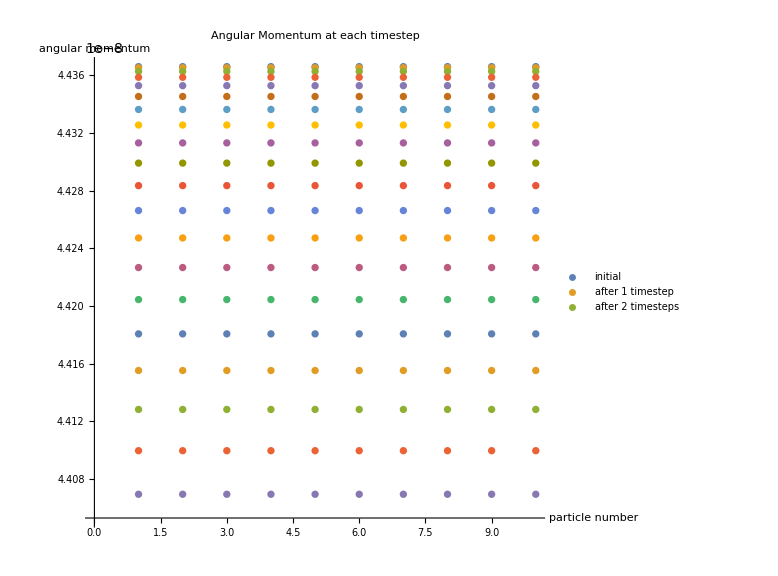

```mathematica
ch2AMgraph = ListPlot[{ch2AM,ch2AM2,ch2AM3,ch2AM4,ch2AM5,ch2AM6,ch2AM7,ch2AM8,ch2AM9,ch2AM10,ch2AM11,ch2AM12,ch2AM13,ch2AM14,ch2AM15,ch2AM16,ch2AM17,ch2AM18,ch2AM19,ch2AM20},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 1 timestep","after 2 timesteps"},AxesLabel->{"particle number","angular momentum"}, PlotLabel-> "Angular Momentum at each timestep"]
```

```mathematica
ch2SDgraph = ListPlot[{ch1SD},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"standard deviation"},AxesLabel->{"timestep","standard deviation of velocity"}, PlotLabel-> "Velocity Dispersion"]
```

-Graphics-

#### Power Spectra

```mathematica
ch2PS1 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",1,1;;4}];
ch2PS2 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",2,1;;4}];
ch2PS3 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",3,1;;4}];
ch2PS4 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",4,1;;4}];
ch2PS5 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",5,1;;4}];
ch2PS6 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",6,1;;4}];
ch2PS7 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",7,1;;4}];
ch2PS8 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",8,1;;4}];
ch2PS9 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",9,1;;4}];
ch2PS10 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",10,1;;4}];
ch2PS11 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",11,1;;4}];
ch2PS12 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",12,1;;4}];
ch2PS13 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",13,1;;4}];
ch2PS14 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",14,1;;4}];
ch2PS15 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",15,1;;4}];
ch2PS16 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",16,1;;4}];
ch2PS17 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",17,1;;4}];
ch2PS18 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",18,1;;4}];
ch2PS19 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",19,1;;4}];
ch2PS20 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",20,1;;4}];
ch2PS21 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",21,1;;4}];
ch2PS81 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",81,1;;4}];
ch2PS82 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",82,1;;4}];
ch2PS83 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",83,1;;4}];
ch2PS84 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",84,1;;4}];
ch2PS85 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",85,1;;4}];
ch2PS86 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",86,1;;4}];
ch2PS87 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",87,1;;4}];
ch2PS88 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",88,1;;4}];
ch2PS89 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",89,1;;4}];
ch2PS90 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",90,1;;4}];
ch2PS91 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",91,1;;4}];
ch2PS92 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",92,1;;4}];
ch2PS93 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",93,1;;4}];
ch2PS94 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",94,1;;4}];
ch2PS95 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",95,1;;4}];
ch2PS96 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",96,1;;4}];
ch2PS97 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",97,1;;4}];
ch2PS98 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",98,1;;4}];
ch2PS99 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",99,1;;4}];
ch2PS100 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",100,1;;4}];
ch2PS101 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",101,1;;4}];
```

```mathematica
ch2FT1 = Abs[Fourier[{ch2PS1}]]^2;
ch2FT2 = Abs[Fourier[{ch2PS2}]]^2;
ch2FT3 = Abs[Fourier[{ch2PS3}]]^2;
ch2FT4 = Abs[Fourier[{ch2PS4}]]^2;
ch2FT5 = Abs[Fourier[{ch2PS5}]]^2;
ch2FT6 = Abs[Fourier[{ch2PS6}]]^2;
ch2FT7 = Abs[Fourier[{ch2PS7}]]^2;
ch2FT8 = Abs[Fourier[{ch2PS8}]]^2;
ch2FT9 = Abs[Fourier[{ch2PS9}]]^2;
ch2FT10 = Abs[Fourier[{ch2PS10}]]^2;
ch2FT11 = Abs[Fourier[{ch2PS11}]]^2;
ch2FT12 = Abs[Fourier[{ch2PS12}]]^2;
ch2FT13 = Abs[Fourier[{ch2PS13}]]^2;
ch2FT14 = Abs[Fourier[{ch2PS14}]]^2;
ch2FT15 = Abs[Fourier[{ch2PS15}]]^2;
ch2FT16 = Abs[Fourier[{ch2PS16}]]^2;
ch2FT17 = Abs[Fourier[{ch2PS17}]]^2;
ch2FT18 = Abs[Fourier[{ch2PS18}]]^2;
ch2FT19 = Abs[Fourier[{ch2PS19}]]^2;
ch2FT20 = Abs[Fourier[{ch2PS20}]]^2;
ch2FT81 = Abs[Fourier[{ch2PS81}]]^2;
ch2FT82 = Abs[Fourier[{ch2PS82}]]^2;
ch2FT83 = Abs[Fourier[{ch2PS83}]]^2;
ch2FT84 = Abs[Fourier[{ch2PS84}]]^2;
ch2FT85 = Abs[Fourier[{ch2PS85}]]^2;
ch2FT86 = Abs[Fourier[{ch2PS86}]]^2;
ch2FT87 = Abs[Fourier[{ch2PS87}]]^2;
ch2FT88 = Abs[Fourier[{ch2PS88}]]^2;
ch2FT89 = Abs[Fourier[{ch2PS89}]]^2;
ch2FT90 = Abs[Fourier[{ch2PS90}]]^2;
ch2FT91 = Abs[Fourier[{ch2PS91}]]^2;
ch2FT92 = Abs[Fourier[{ch2PS92}]]^2;
ch2FT93 = Abs[Fourier[{ch2PS93}]]^2;
ch2FT94 = Abs[Fourier[{ch2PS94}]]^2;
ch2FT95 = Abs[Fourier[{ch2PS95}]]^2;
ch2FT96 = Abs[Fourier[{ch2PS96}]]^2;
ch2FT97 = Abs[Fourier[{ch2PS97}]]^2;
ch2FT98 = Abs[Fourier[{ch2PS98}]]^2;
ch2FT99 = Abs[Fourier[{ch2PS99}]]^2;
ch2FT100 = Abs[Fourier[{ch2PS100}]]^2;

ch2PSgraph =  ListPlot[{ch2FT1,ch2FT2,ch2FT3,ch2FT4,ch2FT5,ch2FT6,ch2FT7,ch2FT8,ch2FT9,ch2FT10,ch2FT11,ch2FT12,ch2FT13,ch2FT14,ch2FT15,ch2FT16,ch2FT17,ch2FT18,ch2FT19,ch2FT20,ch2FT100},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 1 timestep","after 2 timesteps"},AxesLabel->{"particle number","angular momentum"}, PlotLabel-> "Angular Momentum at each timestep"]
```

-Graphics-

### Version 3: Same timestep, fewer particles NFW parameters = {417.0 * pow(10,3) * mau * secyr, 36.54 * kpcau, 90.0 * pi / 180, 1.0, 1.0, 1.0} (NO TRIAXIALITY) 10 test particles r0 = 15 kpc 100 timesteps of 1,000, 000 years each

```mathematica
ch3pos1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",1;;10,1;;2}];
ch3pos2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",10;;20,1;;2}];
ch3pos3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",20;;30,1;;2}];
ch3pos4 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",30;;40,1;;2}];
ch3pos5 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",40;;50,1;;2}];
ch3pos6 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",50;;60,1;;2}];
ch3pos7 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",60;;70,1;;2}];
ch3pos8 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",70;;80,1;;2}];
ch3pos9 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",80;;90,1;;2}];
ch3pos10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",90;;100,1;;2}];
ch3pos11 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",100;;110,1;;2}];
ch3pos12 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",110;;120,1;;2}];
ch3pos13 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",120;;130,1;;2}];
ch3pos14 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",130;;140,1;;2}];
ch3pos15 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",140;;150,1;;2}];
ch3pos16 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",150;;160,1;;2}];
ch3pos17 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",160;;170,1;;2}];
ch3pos18 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",170;;180,1;;2}];
ch3pos19 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",180;;190,1;;2}];
ch3pos20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",190;;200,1;;2}];
ch3pos21 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",200;;210,1;;2}];
ch3pos22 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",210;;220,1;;2}];
ch3pos23 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",220;;230,1;;2}];
ch3pos24 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",230;;240,1;;2}];
ch3pos25 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",240;;250,1;;2}];
ch3pos26 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",250;;260,1;;2}];
ch3pos27 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",260;;270,1;;2}];
ch3pos28 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",270;;280,1;;2}];
ch3pos29 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",280;;290,1;;2}];
ch3pos30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",290;;300,1;;2}];
ch3pos31 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",300;;310,1;;2}];
ch3pos32 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",310;;320,1;;2}];
ch3pos33 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",320;;330,1;;2}];
ch3pos34 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",330;;340,1;;2}];
ch3pos35 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",340;;350,1;;2}];
ch3pos36 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",350;;360,1;;2}];
ch3pos100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",990;;1000,1;;2}];
```

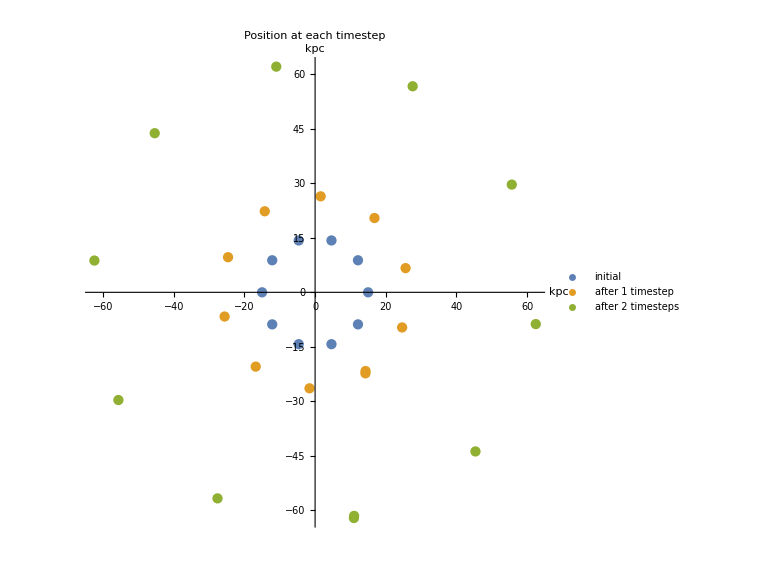

```mathematica
ch3posgraph = ListPlot[{ch3pos1,ch3pos35,ch3pos100},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 1 timestep","after 2 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

### Version 4: timestep/100, fewer particles NFW parameters = {417.0 * pow(10,3) * mau * secyr, 36.54 * kpcau, 90.0 * pi / 180, 1.0, 1.0, 1.0} (NO TRIAXIALITY) 10 test particles r0 = 15 kpc 100 timesteps of 10,000 years each

```mathematica
ch4pos1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",1;;10,1;;2}];
ch4pos2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",10;;20,1;;2}];
ch4pos3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",20;;30,1;;2}];
ch4pos4 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",30;;40,1;;2}];
ch4pos5 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",40;;50,1;;2}];
ch4pos6 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",50;;60,1;;2}];
ch4pos7 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",60;;70,1;;2}];
ch4pos8 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",70;;80,1;;2}];
ch4pos9 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",80;;90,1;;2}];
ch4pos10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",90;;100,1;;2}];
ch4pos11 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",100;;110,1;;2}];
ch4pos12 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",110;;120,1;;2}];
ch4pos13 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",120;;130,1;;2}];
ch4pos14 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",130;;140,1;;2}];
ch4pos15 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",140;;150,1;;2}];
ch4pos16 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",150;;160,1;;2}];
ch4pos17 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",160;;170,1;;2}];
ch4pos18 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",170;;180,1;;2}];
ch4pos19 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",180;;190,1;;2}];
ch4pos20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",190;;200,1;;2}];
ch4pos21 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",200;;210,1;;2}];
ch4pos22 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",210;;220,1;;2}];
ch4pos23 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",220;;230,1;;2}];
ch4pos24 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",230;;240,1;;2}];
ch4pos25 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",240;;250,1;;2}];
ch4pos26 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",250;;260,1;;2}];
ch4pos27 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",260;;270,1;;2}];
ch4pos28 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",270;;280,1;;2}];
ch4pos29 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",280;;290,1;;2}];
ch4pos30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",290;;300,1;;2}];
ch4pos31 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",300;;310,1;;2}];
ch4pos32 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",310;;320,1;;2}];
ch4pos33 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",320;;330,1;;2}];
ch4pos34 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",330;;340,1;;2}];
ch4pos35 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",340;;350,1;;2}];
ch4pos36 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",350;;360,1;;2}];
ch4pos100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",990;;1000,1;;2}];
```

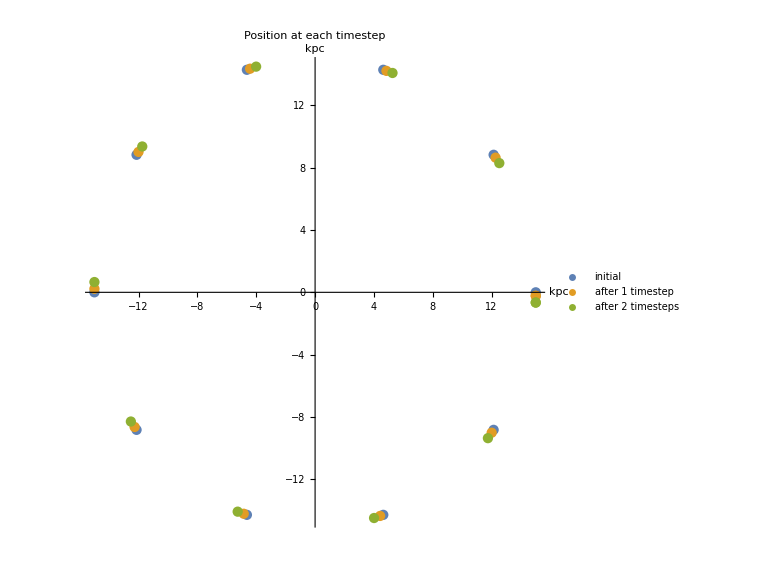

```mathematica
ch4posgraph = ListPlot[{ch4pos1,ch4pos35,ch4pos100},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 1 timestep","after 2 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

### Version 5: less massive gravity, same timestep NFW parameters = {200.0 * pow(10,3) * mau * secyr, 36.54 * kpcau, 90.0 * pi / 180, 1.0, 1.0, 1.0} (NO TRIAXIALITY) 10 test particles r0 = 15 kpc 100 timesteps of 1,000, 000 years each

```mathematica
ch5pos1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",1;;10,1;;2}];
ch5pos2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",10;;20,1;;2}];
ch5pos3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",20;;30,1;;2}];
ch5pos4 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",30;;40,1;;2}];
ch5pos5 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",40;;50,1;;2}];
ch5pos6 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",50;;60,1;;2}];
ch5pos7 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",60;;70,1;;2}];
ch5pos8 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",70;;80,1;;2}];
ch5pos9 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",80;;90,1;;2}];
ch5pos10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",90;;100,1;;2}];
ch5pos11 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",100;;110,1;;2}];
ch5pos12 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",110;;120,1;;2}];
ch5pos13 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",120;;130,1;;2}];
ch5pos14 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",130;;140,1;;2}];
ch5pos15 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",140;;150,1;;2}];
ch5pos16 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",150;;160,1;;2}];
ch5pos17 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",160;;170,1;;2}];
ch5pos18 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",170;;180,1;;2}];
ch5pos19 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",180;;190,1;;2}];
ch5pos20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",190;;200,1;;2}];
ch5pos21 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",200;;210,1;;2}];
ch5pos22 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",210;;220,1;;2}];
ch5pos23 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",220;;230,1;;2}];
ch5pos24 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",230;;240,1;;2}];
ch5pos25 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",240;;250,1;;2}];
ch5pos26 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",250;;260,1;;2}];
ch5pos27 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",260;;270,1;;2}];
ch5pos28 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",270;;280,1;;2}];
ch5pos29 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",280;;290,1;;2}];
ch5pos30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",290;;300,1;;2}];
ch5pos31 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",300;;310,1;;2}];
ch5pos32 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",310;;320,1;;2}];
ch5pos33 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",320;;330,1;;2}];
ch5pos34 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",330;;340,1;;2}];
ch5pos35 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",340;;350,1;;2}];
ch5pos36 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",350;;360,1;;2}];
ch5pos100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",990;;1000,1;;2}];
ch5posgraph = ListPlot[{ch4pos1,ch4pos35,ch4pos100},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 1 timestep","after 2 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

Import::nffil: File /Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv not found during Import.

-Graphics-